Wolfram Online Mini Campus. Part 9

Instagram Posts
Pinterest Posts
"Translation" of SageMath Online Mini Campus. Part 9

Graphs as Playgrounds

```mathematica
DG=GraphData["DesarguesGraph","Graph","All"];
PT={ "Classic","Business","Detailed",
"Scientific","Minimal","Web","Marketing"};
Multicolumn[Table[GraphPlot[DG[[i]],
PlotTheme->PT[[i]],PlotLabel->PT[[i]]],{i,7}],4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

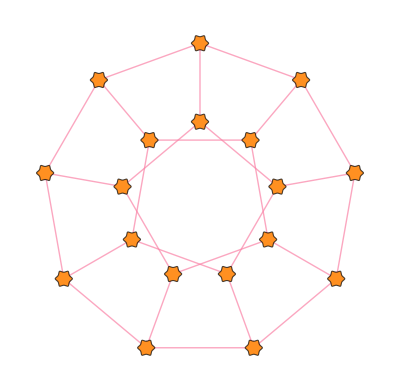
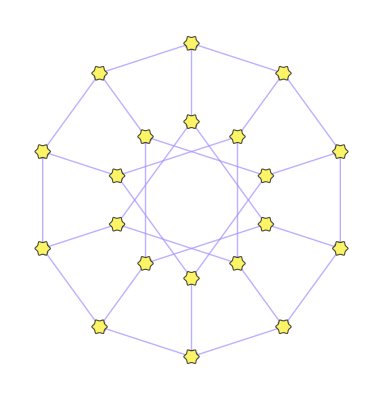
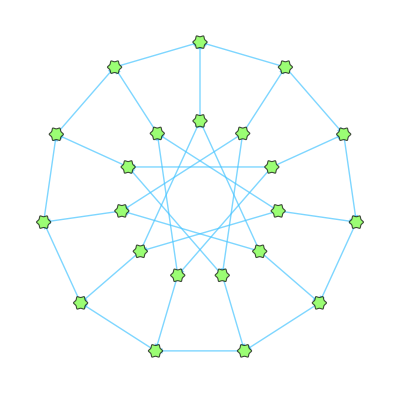
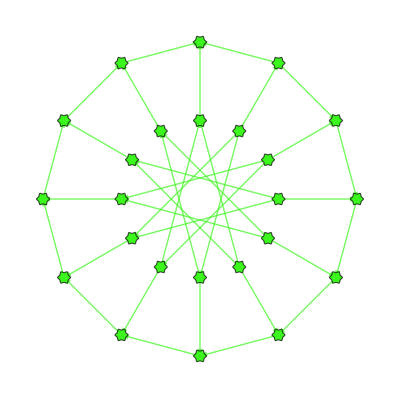

```mathematica
RF=Function[{p},Rescale[p/16,{.5,1}]]; 
CF=Function[{p},ColorData["BrightBands"][p]];
CPG[n_]:=GraphPlot[PetersenGraph[n,7],
VertexStyle->CF[1-RF[n]],VertexShapeFunction->"ConcaveHexagon",
VertexSize->.3,EdgeStyle->CF[RF[n]],EdgeShapeFunction->"CarvedArrow"];
Table[CPG[N],{N,{9,10,11,12}}]
```

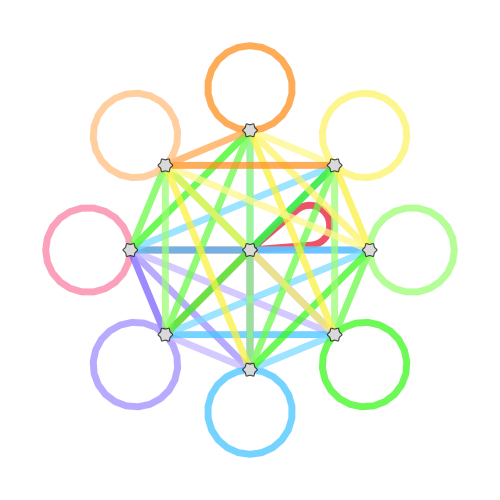

```mathematica
ERF[weights_]:={ColorData["BrightBands"][Rescale[weights[[Sequence@@#2]],
{Min@weights,Max@weights}]],Thickness[0.01],Opacity[0.75],Arrow[#1]}&;
GP[weights_]:=GraphPlot[WeightedAdjacencyGraph[weights],
Method -> "StarEmbedding",VertexStyle->LightGray,
VertexSize->.15,VertexShapeFunction->"ConcaveHexagon",
EdgeRenderingFunction->(ERF[weights]),ImageSize->500]
GP[SparseArray[{i_,j_}:>i+j,{9,9}]]
```

```mathematica
Manipulate[CompleteGraph[12,
EdgeStyle->Flatten[Table[Table[k<->j->Hue[k/12],
{k,12}],{j,2,V}]],
VertexStyle->Flatten[Table[k->Hue[k/12],{k,12}]]],
{V,Range[12,2,-1]}]
```

Vectors and Vector Fields as Playgrounds

```mathematica
Manipulate[With[{f={Sin[k1*t],Cos[k2*t]+Cos[k3*t]}},
Show[Table[Graphics[{Hue[t/100],
Arrow[{{Sin[t],Cos[t]},
f+{Sin[t],Cos[t]}}]}],
{t,0,100Pi}],ImageSize->{500,500}]],
{k1,Range[1,5,1]},{k2,Range[5,9,1]},{k3,Range[4,8,1]}]
```

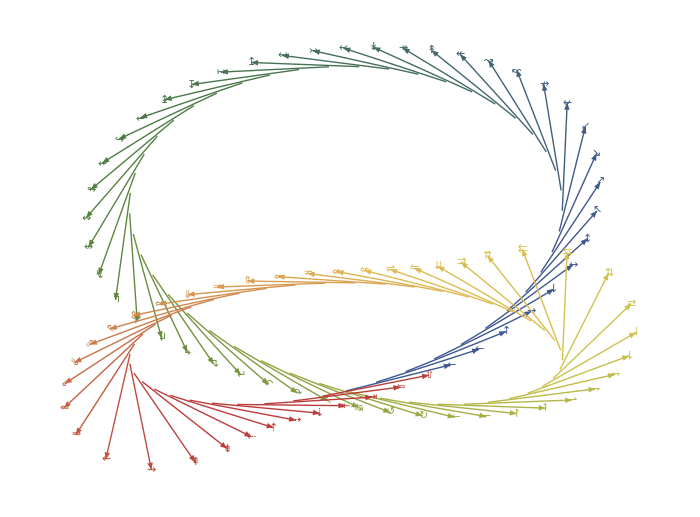

```mathematica
MF=CharacterRange["←","⇿"];
CF2=Function[{p},ColorData["DarkRainbow"][p]];
With[{g={2Sin[2x],Sin[x]-Cos[2x]}},
Show[ Graphics[Table[{CF2[t/(2Pi)],
Arrowheads[{{.001,1}}],Arrow[{g,Normalize[D[g,x]]+g}],
Text[Style[MF[[Floor[14t+1]]],Large],Normalize[D[g,x]]+g]}/.x->t,
{t,0,2Pi,.07}]],ImageSize->700]]
```

```mathematica
AH=Arrowheads[{{.11,1,-Graphics-}}, Appearance -> "Projected"];
Graphics3D[{AH,Arrow[Table[{{i*Sin[i]/2,i*Cos[i],.01},{i*Sin[i]/2,i*Cos[i],0.2}},{i,-4,4,1}]],
                       Darker[Brown],Cuboid[{-2,-4,-2.5},{2,4,-2}]},Boxed->False]
```

-Graphics3D-

Complex Numbers as Playgrounds

```mathematica
Manipulate[ComplexPlot[z^4+1/z^4,
{z,-1.4-1.4 I,1.4+1.4 I},ColorFunction->colfun,ImageSize->500],
{colfun,{"CyclicLogAbs","CyclicLogAbsArg",
"ShiftedCyclicLogAbs","CyclicReImLogAbs"}}]
```

```mathematica
DensityPlot[Arg[(x+I y)^4+1/(x+I y)^4],
{x,-1.4,1.4},{y,-1.4,1.4},PlotPoints->200,
ColorFunction->(Hue[#/(2 Pi)] &),
ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

```mathematica
Manipulate[ComplexPlot[z^3-z^2+1/z,{z,-1.4-1.4 I,1.4+1.4 I},
PlotPoints->50,Mesh->Automatic, MeshStyle->{Gray,White},
ImageSize->500,MeshFunctions->meshfunction],{meshfunction,
{{Log10[Abs[#2]]&,Arg[#2]&},{Abs[Re[#2]]^.5&,Abs[Im[#2]]^.5&},
{Cos[#2]^.01&,Sin[#2]^.01&},
{Cos[Log10[Abs[#2]]]&,Sin[Log10[Abs[#2]]]&}}}]
```

Inequalities as Playgrounds

```mathematica
RegionPlot[Cos[x^7+y^7]≤.05,{x,-4,4},{y,-4,4},
PlotPoints->100,BoundaryStyle->None,ImageSize->500,
ColorFunction->Function[{x,y},
ColorData["BrightBands"][Abs[x-y]]]]
```

-Graphics-

```mathematica
RegionPlot[Sin[4x^3*y]Cos[4y^3*x]<.1,{x,-4,4},{y,-4,4},
PlotPoints->100,BoundaryStyle->Gray,ImageSize->500,
PlotStyle->Texture[ExampleData[{"ColorTexture",
"MultiSpiralsPattern"}]]]
```

-Graphics-

HTML Objects as Playgrounds

```mathematica
EmbeddedHTML["<style>text {font-size:400%;}
emoji {margin:0; color:transparent; text-shadow:0 0 7px #3636ff; font-size:400%; position:relative;}
emoji::before {content:attr(title); position:absolute; text-shadow:0 0 0 #fff;}</style>
<emoji title='&#x1F985'>&#x1F310</emoji> <text>&nbsp; &#x1F985</text> <br></br> 
<emoji title='&#x1F3A1'>&#x1F3A1</emoji> <text>&nbsp; &#x1F3A1</text><br></br> 
<emoji title='&#x1F3A0'>&#x1F3A1</emoji> <text>&nbsp; &#x1F3A0</text>"]
```

Null<style>text {font-size:400%;}
emoji …</emoji> <text>&nbsp; &#x1F3A0</text><style>text {font-size:400%;}
emoji {margin:0; color:transparent; text-shadow:0 0 7px #3636ff; font-size:400%; position:relative;}
emoji::before {content:attr(title); position:absolute; text-shadow:0 0 0 #fff;}</style>
<emoji title='&#x1F985'>&#x1F310</emoji> <text>&nbsp; &#x1F985</text> <br></br> 
<emoji title='&#x1F3A1'>&#x1F3A1</emoji> <text>&nbsp; &#x1F3A1</text><br></br> 
<emoji title='&#x1F3A0'>&#x1F3A1</emoji> <text>&nbsp; &#x1F3A0</text>